DEVBIO 232 Homework 1
January 31st, 2019
Samuel Morabito

#### Problem 1: Simple Production Destruction Model

```mathematica
(* reset button for all variables *)
ClearAll["Global`*"]
```

Problem 1b:

```mathematica
system= {
A'[t] == p-r A[t], A[0]==Azero
};

(* getting the exact symbolic solution *)
sol1 = DSolve[system,A[t],t]
```

{{A[t]→(ⅇ^(-r t) (-p+ⅇ^(r t) p+Azero r))/r}}

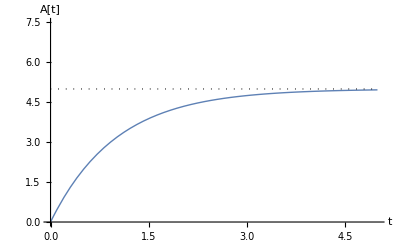

```mathematica
(* plot the solution *)
parameters1 = {p-> 5, Azero-> 0, r->1};
case1 = sol1 /.parameters1;

p1 = Plot[{A[t]/.case1},{t,0,5},PlotStyle->Thick,PlotRange->{0,7.5},AxesLabel->{"t","A[t]"}];
l1 = Graphics[{Dotted, Line[{{0,5},{5,5}}]}];
Show[p1,l1]
```

#### Problem 1c:

```mathematica
Manipulate[
parameters2= {p->pValue,Azero-> 0, r-> rValue};
Plot[{A[t]/.sol1/.parameters2},{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"t","A[t]"}],
{pValue,0.2,10}, {rValue, 0.2,10}
]
```

#### Problem 2: Simple Transport Model

```mathematica
system2= {
mb'[t] == -Subscript[k, 1] mb[t], mb[0]== mbzero,
cy'[t] == Subscript[k, 1] mb[t] - Subscript[k, 2] cy[t], cy[0] == 0,
nu'[t] == 76799999 Subscript[k, 2] cy[t], nu[0] == 0
};

(* getting the exact symbolic solution *)
sol2 = DSolve[system2,{mb[t], cy[t], nu[t]}, t]
```

{{cy[t]→-(ⅇ^(-t k_1-t k_2) (-ⅇ^(t k_1)+ⅇ^(t k_2)) mbzero k_1)/(k_1-k_2),mb[t]→ⅇ^(-t k_1) mbzero,nu[t]→(ⅇ^(-t k_1-t k_2) mbzero (-ⅇ^(t k_1) k_1+ⅇ^(t k_1+t k_2) k_1+ⅇ^(t k_2) k_2-ⅇ^(t k_1+t k_2) k_2))/(k_1-k_2)}}

Problem 2b:

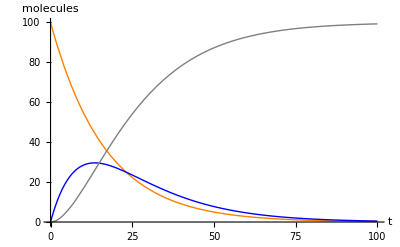

```mathematica
(* plot the solution *)
parameters2 = {Subscript[k, 1]-> 0.06, Subscript[k, 2]-> 0.09, mbzero-> 100};
case2 = sol2 /.parameters2;

p1 = Plot[{mb[t]/.case2},{t,0,100},PlotStyle->{Orange,Thick}, PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p2 = Plot[{cy[t]/.case2},{t,0,100},PlotStyle->{Blue,Thick},PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p3 = Plot[{nu[t]/.case2},{t,0,100},PlotStyle->{Gray,Thick},PlotRange->{0,100},AxesLabel->{"t","molecules"}];
Show[p1,p2,p3]
```

Problem 2c:

```mathematica
Manipulate[
parameters2 = {Subscript[k, 1]-> k1value, Subscript[k, 2]-> k2value, mbzero-> startingMolecules};
case2 = sol2 /.parameters2;

p1 = Plot[{mb[t]/.case2},{t,0,100},PlotStyle->{Orange,Thick},AxesLabel->{"t","molecules"}];
p2 = Plot[{cy[t]/.case2},{t,0,100},PlotStyle->{Blue,Thick},AxesLabel->{"t","molecules"}];
p3 = Plot[{nu[t]/.case2},{t,0,100},PlotStyle->{Gray,Thick},AxesLabel->{"t","molecules"}];
Show[p1,p2,p3],
{k1value, 0.001,10},{k2value, 0.001, 10}, {startingMolecules, 10, 10000}
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ⅇ^(-0.002 t) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ⅇ^(-0.002 t) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ⅇ^(-0.002 t) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ⅇ^(-0.002 t) ComplexInfinity encountered.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Problem 2d:

```mathematica
parameters2 = {Subscript[k, 1]-> 0.06, Subscript[k, 2]-> 0.09, mbzero-> 100};
ncase2 = system2 /.parameters2;
nsol2 = NDSolve[ncase2,{mb[t], cy[t], nu[t]}, {t,0,10}]
```

{{mb[t]→InterpolatingFunction[…][t],cy[t]→InterpolatingFunction[…][t],nu[t]→InterpolatingFunction[…][t]}}

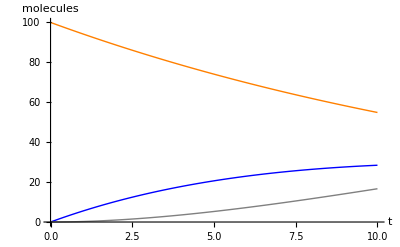

```mathematica
p1 = Plot[{mb[t]/.nsol2},{t,0,10},PlotStyle->{Orange,Thick}, PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p2 = Plot[{cy[t]/.nsol2},{t,0,10},PlotStyle->{Blue,Thick},PlotRange->{0,100},AxesLabel->{"t","molecules"}];
p3 = Plot[{nu[t]/.nsol2},{t,0,10},PlotStyle->{Gray,Thick},PlotRange->{0,100},AxesLabel->{"t","molecules"}];
Show[p1,p2,p3]
```